```mathematica
Clear[Ra1, Ra2, Rb1, Rb2, Rc1, Rc2, k, c,pointA, pointB, pointC, point1,point2,A,B,P1,P2,mat,noise,sol,p]
```

```mathematica
pointA={0,-1};
pointB={0,1};
pointC={20,0};
point1={5,-.1};
point2={5,.1};
Ra1=EuclideanDistance[pointA,point1];
Ra2=EuclideanDistance[pointA,point2];
Rb1=EuclideanDistance[pointB,point1];
Rb2=EuclideanDistance[pointB,point2];
Rc1=EuclideanDistance[pointC,point1];
Rc2=EuclideanDistance[pointC,point2];
f=1000;
k=2Pi f/343;
c=1;
mat ={{1/Ra1* E^(-I k Ra1), 1/Rb1* E^(-I k Rb1)},{1/Ra2 *E^(-I k Ra2), 1/Rb2 *E^(-I k Rb2)}};
noise=c{{1/Rc1 *E^(-I k Rc1)},{1/Rc2* E^(-I k Rc2)}};
sol=- Inverse[mat].noise;
p=mat.sol+noise;
A=Part[sol,1,1];
B=Part[sol,2,1];
pfunc[x_,y_]:=A/(Sqrt[(pointA[[1]]-x)^2+(pointA[[2]]-y)^2])*E^(-I k Sqrt[(pointA[[1]]-x)^2+(pointA[[2]]-y)^2])+B/(Sqrt[(pointB[[1]]-x)^2+(pointB[[2]]-y)^2])*E^(-I k Sqrt[(pointB[[1]]-x)^2+(pointB[[2]]-y)^2])+c/(Sqrt[(pointC[[1]]-x)^2+(pointC[[2]]-y)^2])*E^(-I k Sqrt[(pointC[[1]]-x)^2+(pointC[[2]]-y)^2]);
pdb[x_]:=20 Log10[x/(20*10^-6)];
Plot3D[pdb[Abs[N[pfunc[x,y]]]],{x,0,20},{y,-10, 10}]
```

-Graphics3D-

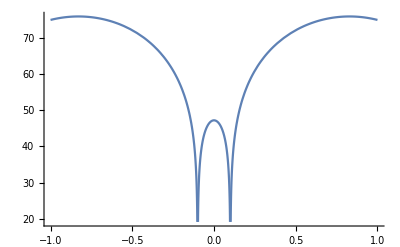

```mathematica
Plot[pdb[Abs[N[pfunc[5,y]]]],{y,-1,1}]
```

```mathematica
A
```

-0.119468-0.136743 ⅈ

```mathematica
"convert to exponential"-0.11946814640693407-0.13674315987600794 ⅈWith[{n=Abs[-0.11946814640693407-0.13674315987600794 ⅈ],a=Arg[-0.11946814640693407-0.13674315987600794 ⅈ]},Defer[n ⅇ^(ⅈ a)]]
```

0.18158 ⅇ^(ⅈ (-2.28887))

```mathematica
B
```

-0.119468-0.136743 ⅈ

```mathematica
"convert to exponential"-0.11946814640693404-0.13674315987600794 ⅈWith[{n=Abs[-0.11946814640693404-0.13674315987600794 ⅈ],a=Arg[-0.11946814640693404-0.13674315987600794 ⅈ]},Defer[n ⅇ^(ⅈ a)]]
```

0.18158 ⅇ^(ⅈ (-2.28887))